```mathematica
A={{Cos[betal]-Cosh[betal],-Sin[betal]+Sinh[betal]},
{12600betal(-Cos[betal]-Cosh[betal])-s k(Sin[betal]-Sinh[betal]),12600 betal(Sin[betal]+Sinh[betal])-s k(-Cos[betal]+Cosh[betal])}}
```

{{Cos[betal]-Cosh[betal],-Sin[betal]+Sinh[betal]},{12600 betal (-Cos[betal]-Cosh[betal])-k s (Sin[betal]-Sinh[betal]),-k s (-Cos[betal]+Cosh[betal])+12600 betal (Sin[betal]+Sinh[betal])}}

```mathematica
a=Det[A]
```

k s Cos[betal]^2-2 k s Cos[betal] Cosh[betal]+k s Cosh[betal]^2-25200 betal Cosh[betal] Sin[betal]-k s Sin[betal]^2+25200 betal Cos[betal] Sinh[betal]+2 k s Sin[betal] Sinh[betal]-k s Sinh[betal]^2

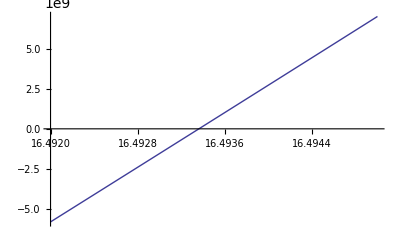

```mathematica
Plot[a/.{s->-1,k->10},{betal,16.492,16.495}]
```